# Comparison between the triangle plaquette model and the triangle continuum model.

# Triangular Plaquette Model H = (2/g^2) E^2 + 2/g^2 B^2 ---> (2/g^2)(E1^2 +E2^2 + E3^2) + (1/g^2) (1 - Cos[theta1, +theta2 + theta3)) With commutators [E_i, e^{itheta_j}] = delta_[ij} e^{itheta_j}

```mathematica
(* All terms are positve: With Wilson Plaq
B^2(s) = (1/2)Tr[2 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:    U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)
```

```mathematica
(*Sigma operators*)
```

```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
SigmaP= (Sigma[1]+ I*Sigma[2])/2;
SigmaM= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
NQubits = 12
```

12

```mathematica
(*  zero point terms ((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit]*)
```

## Plaquette term

```mathematica
(*Single plaquette term at s-th layer *)
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

{6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

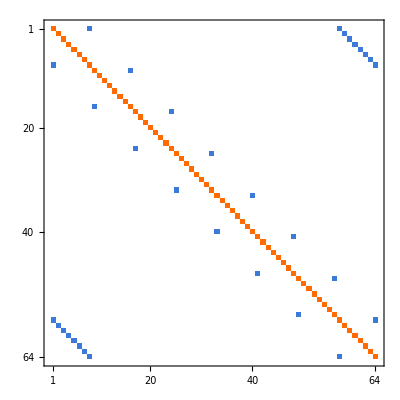

```mathematica
Bsingle[s_, nQubit_] :=KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]];
(*Sum over all layers*)
B[nQubit_] := - Sum[Bsingle[s, nQubit],{s,1,nQubit/3}]  + (nQubit/3)  IdentityMatrix[2^nQubit]
Eigenvalues[B[6]]
Eigenvalues[B[9]]
MatrixPlot[B[6]]
```

## Electric links between neighborhood layers sigmaz_{j + 3} x sigmaz_j note + convention on Qubit operators

```mathematica
Es[nQubit_] :=   Sum[FullSigma[3,Mod[j+3,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] +  (nQubit - 6 Mod[nQubit,2])*IdentityMatrix[2^nQubit]
Eigenvalues[Es[6]]
```

{12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0}

## XX + YY chain

Eigenvalues[SparseArrayXY[6]]

Eigenvalues[SparseArrayXY[9]]

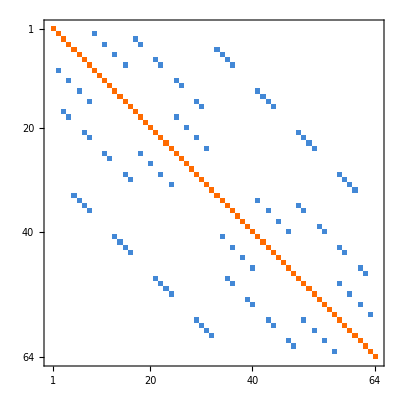

```mathematica
XY[nQubit_] :=- Sum[FullSigma[1,Mod[j+3,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
- Sum[FullSigma[2,Mod[j+3,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]  + 2 nQubit * IdentityMatrix[2^nQubit] 
Eigenvalues[SparseArrayXY[6]]
Eigenvalues[SparseArrayXY[9]]
MatrixPlot[XY[6]]
```

## Define Hamiltonian

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
(* H0[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]
H1[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]+
((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit] *)
```

```mathematica
H[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*Es[nQubit] + (1/(2*g^2))* B[nQubit]]+  (alpha/(2*g^2))*XY[nQubit]
```

```mathematica
Eigenvalues[Es[6]]
```

{12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[B[6]]
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

```mathematica
Eigenvalues[XY[6]]
```

{24,20,20,20,20,20,20,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,0}

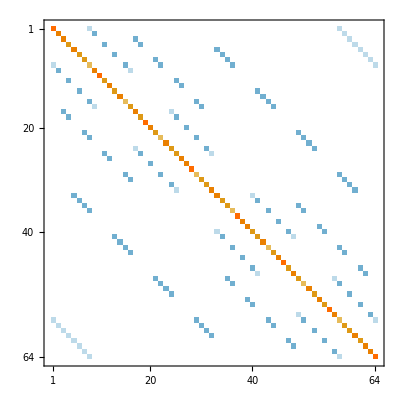

```mathematica
MatrixPlot[H[1, 1, 6]]
```

## Eigenvalue spectrum of H(g, alpha)

```mathematica
Eigs[g_, alpha_, nQubit_, k_] := Sort[Eigenvalues[H[g, alpha, nQubit], k], Less]
```

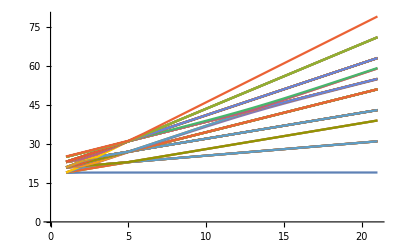

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

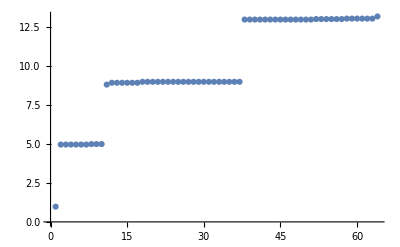

```mathematica
ListPlot[Eigs[1, 1,6 , 2^6]]
```

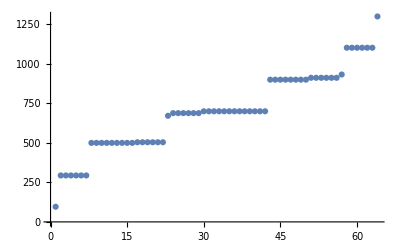

```mathematica
ListPlot[Eigs[0.1, 1,6 , 2^6]]
```

# Gauge Rotation Operators

```mathematica
(* Gauge Rotation Operators J12, J23, J31 *)
J12[nQubit_] := Sum[FullSigma[3,Mod[s*3+1,nQubit], nQubit]-FullSigma[3, Mod[s*3+2,nQubit], nQubit],{s,0,nQubit/3-1}]
J23[nQubit_] := Sum[FullSigma[3,Mod[s*3+2,nQubit], nQubit]-FullSigma[3, Mod[s*3+3,nQubit], nQubit],{s,0,nQubit/3-1}]
J31[nQubit_] := Sum[FullSigma[3,Mod[s*3+3,nQubit], nQubit]-FullSigma[3, Mod[s*3+1,nQubit], nQubit],{s,0,nQubit/3-1}]
```

## Eigenvalues (Diagonal Elements) of Gauge Rotation Operators

```mathematica
D12 = Normal[Diagonal[J12[NQubits]]];
```

```mathematica
D23 = Normal[Diagonal[J23[NQubits]]];
```

```mathematica
D31 = Normal[Diagonal[J31[NQubits]]];
```

```mathematica
(*Check if they sum up to zero *)
```

```mathematica
D12 + D23 + D31
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Sort[D12^2+  D23 ^2 + D31^2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,128,128,128,128,128,128}

## Permutation Rule Ordered by Square Sum Eigenvalues

```mathematica
perm = Ordering[D12^2+ D23^2+D31^2];
```

```mathematica
(* Count the number of zeros *)
```

```mathematica
NZero = Count[D12^2+ D23^2+D31^2, 0]
```

346

## The Permutated Hamiltonian Looks It Consists of Block Sectors with Sub-square Matrices

```mathematica
PermHamiltonian[g_, alpha_, nQubits_] := H[g, alpha, nQubits][[perm, perm]]
```

```mathematica
MatrixPlot[PermHamiltonian[1, 1, NQubits]]
```

-Graphics-

## The sub matrix with basis corresponding to zero eigenvalues

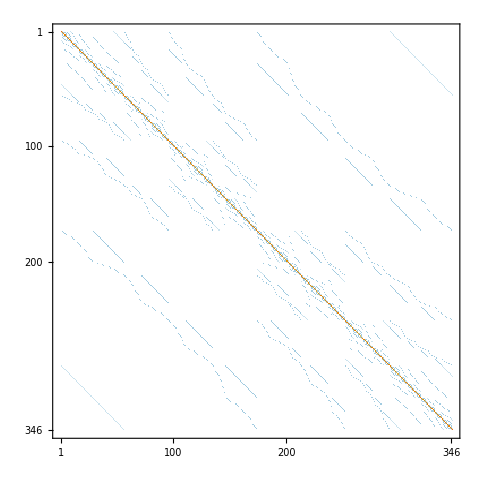

```mathematica
ZeroHamiltonian[g_, alpha_, nQubits_]  := PermHamiltonian[g, alpha, nQubits][[1;;NZero, 1;;NZero]]
ZeroH = ZeroHamiltonian[1, 1, NQubits];
MatrixPlot[ZeroH]
```

## Eigenvalue Spectrum of the Sub-Hamiltonian

```mathematica
Eigenvalues[ZeroH]//N
```

{26.2059,26.1853,26.117,26.0705,26.0419,24.6852,24.6852,24.3255,24.3255,24.3255,24.3255,24.0952,24.0952,24.0853,24.0853,24.0853,24.0853,24.0153,24.0153,24.0047,23.8174,23.8174,23.8174,23.8174,23.4621,23.4621,22.9942,22.8128,22.8128,22.5271,22.5271,22.5225,22.426,22.4107,22.351,22.278,22.278,22.2629,22.2629,22.2568,22.2568,22.1616,22.1616,22.1574,22.1574,22.0616,22.0616,22.0597,22.0597,22.0597,22.0597,22.0465,22.0465,22.0285,22.0285,22.0213,22.0212,22.0211,22.0211,22.0209,22.0157,22.0157,22.0007,22.0007,22.0007,22.0007,22.,22.,22.,21.9181,21.9181,21.911,21.911,21.8698,21.7682,21.7682,21.763,21.763,21.6721,21.6721,21.5991,21.5938,21.5754,21.3189,21.3189,21.3053,21.,21.,20.5754,20.5754,20.5754,20.5754,20.4004,20.4004,20.3622,20.3622,20.3622,20.3622,20.3205,20.3205,20.293,20.293,20.1917,20.1917,20.1917,20.1917,20.1101,20.1101,20.1101,20.1101,20.0806,20.0802,20.0802,20.0597,20.0597,20.0536,20.0536,20.0536,20.0536,20.0435,20.0258,20.0258,20.0163,20.0163,20.015,20.015,20.015,20.015,20.0136,20.0136,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,19.878,19.878,19.878,19.878,19.8728,19.8728,19.8162,19.8162,19.7885,19.7885,19.7527,19.748,19.748,19.726,19.6584,19.6584,19.6508,19.6508,19.6508,19.6508,19.463,19.463,19.463,19.463,19.,19.,18.5555,18.5555,18.498,18.4804,18.4804,18.449,18.449,18.4244,18.4244,18.3121,18.2661,18.2661,18.2592,18.2592,18.2264,18.2264,18.225,18.1672,18.1492,18.0779,18.0598,18.0538,18.0538,18.0153,18.0153,18.0101,18.0101,18.0101,18.0101,18.0073,18.0073,18.0073,18.0073,18.,17.9895,17.9649,17.9649,17.9403,17.9403,17.9402,17.9385,17.9385,17.9384,17.9384,17.9336,17.92,17.9047,17.9047,17.9015,17.9015,17.8708,17.8683,17.8683,17.8559,17.8559,17.8433,17.8433,17.8433,17.8433,17.8387,17.8387,17.8387,17.8387,17.8177,17.7861,17.7861,17.7272,17.7271,17.7271,17.6248,17.6248,17.5903,17.5903,17.5764,17.5666,17.5666,17.5599,17.5599,16.456,16.456,16.456,16.456,16.3615,16.3615,16.1952,16.1952,16.082,16.,16.,16.,16.,15.9908,15.9908,15.9845,15.9845,15.981,15.981,15.981,15.981,15.9789,15.9789,15.9782,15.9782,15.9685,15.9685,15.9685,15.9685,15.9588,15.9588,15.9228,15.9228,15.9228,15.9228,15.9194,15.8943,15.8943,15.8907,15.8786,15.8786,15.8165,15.7966,15.7827,15.7827,15.7715,15.7672,15.7672,15.5187,15.5187,15.5187,15.5187,15.5056,15.5056,14.294,13.9942,13.9942,13.993,13.993,13.9917,13.9917,13.9917,13.9917,13.9894,13.9837,13.9837,13.9791,13.9714,13.9519,13.9468,13.9468,13.9468,13.9468,13.8526,13.8526,13.7262,13.7262,13.6576,11.9901,11.9901,11.9895,11.9895,11.9813,11.9813,11.9267,11.9267,11.9267,11.9267,11.9254,11.8703,9.98302,9.98302,9.94133,7.93864}

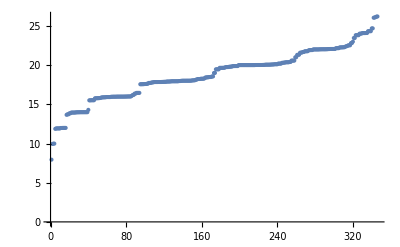

```mathematica
ListPlot[Sort[N[Eigenvalues[Normal[ZeroH]]]]]
```

## What if we change the value of g?

```mathematica
EigenSpectra:= Sort[Eigenvalues[ZeroHamiltonian[0.1, 1.0, NQubits]]]
EigenSpectra//N
lambda0= EigenSpectra [[1]]//N
lambda1 = EigenSpectra [[2]]//N
(1/(lambda1 - lambda0))( EigenSpectra+ lambda1 - 2 lambda0)//N
```

{535.149,797.444,800.019,818.185,818.185,818.185,818.185,824.33,825.464,828.645,828.645,831.738,831.738,831.745,831.745,962.712,962.712,982.146,982.146,995.389,995.389,995.389,995.389,996.465,996.465,996.465,996.465,1046.2,1068.37,1068.37,1069.3,1069.9,1069.9,1092.08,1092.08,1103.89,1103.91,1104.,1111.01,1111.01,1111.01,1111.01,1111.08,1111.08,1111.39,1111.39,1111.39,1111.39,1111.7,1111.7,1114.81,1114.81,1114.95,1114.95,1114.97,1114.97,1115.55,1115.55,1115.69,1115.69,1115.94,1115.94,1115.94,1115.94,1116.5,1116.72,1117.19,1117.2,1117.2,1122.82,1122.83,1122.83,1126.17,1126.17,1126.17,1126.17,1144.04,1144.04,1177.79,1177.79,1179.29,1179.74,1191.02,1191.02,1191.62,1191.62,1192.41,1192.41,1194.4,1194.4,1196.91,1196.91,1197.44,1199.5,1200.06,1202.8,1202.99,1202.99,1210.77,1210.77,1213.71,1213.71,1229.01,1236.13,1236.13,1239.85,1239.85,1244.76,1300.06,1300.06,1321.81,1321.81,1321.81,1321.81,1341.79,1341.79,1341.79,1341.79,1346.77,1346.77,1350.05,1350.05,1364.97,1364.97,1364.97,1364.97,1371.81,1371.81,1371.81,1371.81,1373.18,1373.18,1380.4,1380.4,1380.4,1380.4,1382.64,1385.36,1385.36,1385.36,1385.36,1386.84,1386.87,1388.24,1388.24,1389.98,1391.19,1391.19,1394.15,1394.15,1396.94,1396.94,1396.94,1396.94,1400.01,1400.02,1400.02,1400.02,1400.03,1400.03,1400.03,1400.03,1400.03,1400.04,1400.04,1400.04,1400.04,1400.04,1400.04,1400.04,1400.04,1400.04,1400.05,1400.05,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1400.06,1405.93,1405.93,1405.93,1405.93,1406.22,1406.3,1406.3,1406.66,1406.66,1414.71,1414.71,1414.71,1414.71,1416.59,1416.59,1417.51,1417.51,1417.51,1417.51,1417.7,1419.25,1419.25,1426.92,1431.45,1431.45,1431.45,1431.45,1435.13,1435.13,1435.13,1435.13,1450.05,1450.05,1458.48,1458.48,1458.48,1458.48,1463.53,1463.53,1477.42,1477.42,1477.42,1477.42,1500.06,1500.06,1539.67,1547.6,1547.6,1558.02,1578.12,1578.12,1579.12,1579.12,1581.72,1589.05,1591.8,1591.8,1598.56,1598.56,1600.06,1600.06,1600.06,1600.56,1600.56,1603.21,1603.21,1604.13,1609.09,1609.09,1611.86,1611.86,1612.58,1613.74,1613.74,1626.46,1671.86,1671.86,1671.86,1671.86,1674.34,1674.34,1674.34,1674.34,1676.15,1676.15,1682.88,1682.88,1682.88,1682.97,1682.97,1683.12,1683.3,1683.3,1683.94,1683.94,1685.11,1685.11,1685.13,1685.13,1685.34,1685.34,1685.34,1685.34,1685.46,1685.48,1685.57,1688.79,1688.79,1688.79,1688.79,1693.73,1693.73,1694.17,1694.17,1696.34,1704.31,1704.31,1709.95,1709.95,1710.73,1710.73,1711.84,1738.58,1741.93,1741.93,1787.1,1796.6,1796.6,1803.25,1803.25,1814.84,1814.84,1814.84,1814.84,1823.69,1823.69,1823.69,1823.69,1923.59,1965.87,1966.42,1966.42,1970.12,1970.12,1970.12,1970.12,1973.28,1973.28,1990.96,1990.96,2008.72,2051.96,2250.18}

535.149

797.444

{1.,2.,2.00982,2.07908,2.07908,2.07908,2.07908,2.1025,2.10683,2.11895,2.11895,2.13075,2.13075,2.13077,2.13077,2.63009,2.63009,2.70418,2.70418,2.75467,2.75467,2.75467,2.75467,2.75877,2.75877,2.75877,2.75877,2.94839,3.03292,3.03292,3.03644,3.03874,3.03874,3.12329,3.12329,3.16833,3.1684,3.16873,3.19547,3.19547,3.19547,3.19547,3.19576,3.19576,3.19692,3.19692,3.19692,3.19692,3.1981,3.1981,3.20996,3.20996,3.2105,3.2105,3.21058,3.21058,3.2128,3.2128,3.21333,3.21333,3.21428,3.21428,3.21428,3.21428,3.21639,3.21725,3.21904,3.21906,3.21906,3.24051,3.24054,3.24054,3.25327,3.25327,3.25327,3.25327,3.32142,3.32142,3.45007,3.45007,3.45578,3.4575,3.50052,3.50052,3.5028,3.5028,3.5058,3.5058,3.51341,3.51341,3.52297,3.52297,3.52499,3.53285,3.53498,3.54541,3.54613,3.54613,3.57581,3.57582,3.58702,3.58702,3.64536,3.67249,3.67249,3.68669,3.68669,3.70539,3.91623,3.91623,3.99916,3.99916,3.99916,3.99916,4.07532,4.07532,4.07532,4.07532,4.0943,4.0943,4.10681,4.10681,4.1637,4.1637,4.1637,4.1637,4.18979,4.18979,4.18979,4.18979,4.19501,4.19501,4.22252,4.22252,4.22252,4.22252,4.23107,4.24143,4.24143,4.24143,4.24143,4.24708,4.24718,4.25241,4.25241,4.25903,4.26367,4.26367,4.27496,4.27496,4.28557,4.28557,4.28557,4.28557,4.29728,4.29733,4.29733,4.29733,4.29738,4.29738,4.29738,4.29738,4.29738,4.2974,4.2974,4.2974,4.2974,4.2974,4.2974,4.2974,4.29741,4.29741,4.29742,4.29742,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.29748,4.31985,4.31985,4.31987,4.31987,4.32095,4.32127,4.32127,4.32264,4.32264,4.35334,4.35334,4.35334,4.35334,4.36048,4.36048,4.36399,4.36399,4.36399,4.36399,4.36474,4.37064,4.37064,4.39989,4.41715,4.41715,4.41715,4.41715,4.43117,4.43117,4.43118,4.43118,4.48807,4.48807,4.52019,4.52019,4.52019,4.52019,4.53947,4.53947,4.59242,4.59242,4.59242,4.59242,4.67873,4.67873,4.82973,4.85996,4.85996,4.8997,4.97632,4.97632,4.98013,4.98013,4.99007,5.018,5.0285,5.0285,5.05427,5.05427,5.05998,5.05998,5.05998,5.06189,5.06189,5.07198,5.07198,5.0755,5.09443,5.09443,5.10498,5.10498,5.1077,5.11214,5.11214,5.16061,5.33371,5.33371,5.33371,5.33371,5.34316,5.34316,5.34316,5.34316,5.35006,5.35006,5.37572,5.37573,5.37573,5.37609,5.37609,5.37665,5.37733,5.37733,5.37976,5.37976,5.38423,5.38423,5.3843,5.3843,5.3851,5.3851,5.3851,5.3851,5.38557,5.38564,5.386,5.39827,5.39827,5.39827,5.39827,5.41711,5.41711,5.41876,5.41876,5.42704,5.45744,5.45744,5.47893,5.47893,5.4819,5.4819,5.48613,5.58808,5.60087,5.60087,5.77308,5.80931,5.80931,5.83463,5.83463,5.87884,5.87884,5.87884,5.87884,5.91258,5.91258,5.91258,5.91258,6.29342,6.45463,6.45671,6.45671,6.47082,6.47082,6.47082,6.47082,6.48287,6.48287,6.5503,6.5503,6.61801,6.78286,7.53856}

# 1D chain XXZ model (I.e. No plaquette term)

## The X term and Y term have the same coefficient: H = \sum_j Jxy*X_jX_{j+1} + Jxy*Y_jY_{j+1} + J_z*Z_jZ_{j+1}

```mathematica
XXZ[jxy_, jz_, nQubit_]:= -jxy*(Sum[FullSigma[1,Mod[j+1,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] + Sum[FullSigma[2,Mod[j+1,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] ) -jz*Sum[FullSigma[3,Mod[j+1,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

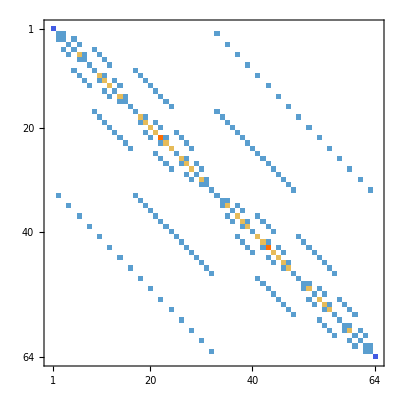

```mathematica
MatrixPlot[XXZ[1, 1, 6]]
```

```mathematica
{evals,evecs}=Eigensystem[XXZ[0.01, 1, 6]];
sortedEigs = SortBy[Transpose[{evals,evecs}],First];
sortedEigs[[1, 2]]
BaseForm[Position[sortedEigs[[1, 2]], _?(Abs[#]>0.01&)], 2]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}

{{1000000_2}}

# Continuum Model Change varables preserving the computors (and redefing charge!) H = (2/g^2)p^2 + (1/g^2) (1 - Cos[theta]) + p12^2 +p23^2 + p31^2 with theta = theta1, +theta2 + theta3 and p = (E1 +E2 + E3)/ 3 External flux/gauge opeartors pij = E_i - E_j

```mathematica
Dia[n_]:= Table[i^2,{i,-n,n}]
Dia[5]
```

{25,16,9,4,1,0,1,4,9,16,25}

# This initializs the matrix for one plaquette, where a is the strength of the magnetic part relative to electric part.

```mathematica
Mat[n_,g_]:=
Table[ (g^2/2)KroneckerDelta[i,j] i^2+ (1/g^2)( 2 KroneckerDelta[i,j] -  KroneckerDelta[i,j+1]-KroneckerDelta[i,j-1]),{i,-n,n},{j,-n,n}]
MatrixForm[Mat[4,g]]
```

(2/g^2+8 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/g^2 | 2/g^2 | -1/g^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+8 g^2)

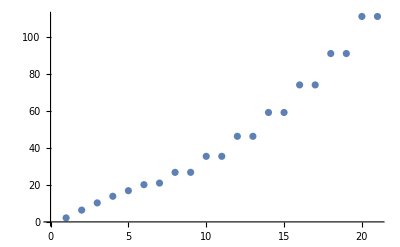

```mathematica
ListPlot[Sort[Re[Eigenvalues[(2/0.795^2)Mat[10,0.795]]],Less]]
```

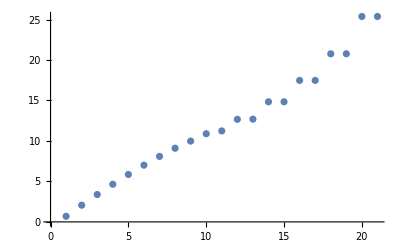

```mathematica
ListPlot[Sort[Re[Eigenvalues[Mat[10,0.6]]],Less]]
```

```mathematica
Dat=Table[Sort[Re[Eigenvalues[Mat[18,g], Method->"Banded"]],Less],{g,0.1,2.1,0.05}];
```

```mathematica
Here one can see how the level degenracy is split as we increase the magnetic term
as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]
```

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.35,-71.08}]

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]

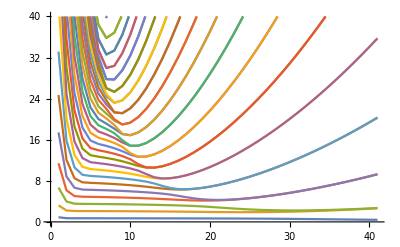

```mathematica
ListPlot[Transpose[Dat], Joined->True,PlotRange->{0,40}]
```

```mathematica
Length[Dat]
```

41

```mathematica
Here is the result with plaquette = 0 and with plaquette = 20, showing that the low energy degrees of freedom have a linear spectrum once magnetic term is strong
```

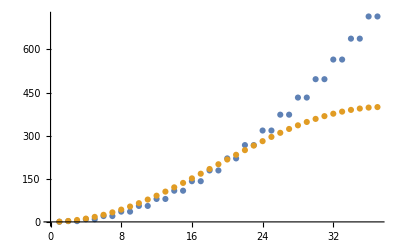

```mathematica
ListPlot[{Dat[[41]],Dat[[1]]}]
```

```mathematica
ListPlot[{Dat[[1]], Sort[Eigenvalues[ZeroHamiltonian[0.1, 1, 6]]]}]
```

Part::partw: Part 71 of {{700.06,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«14»},«49»,«14»} does not exist.

Part::take: Cannot take positions 1 through 346 in {{700.06,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«14»},«49»,«14»}⟦{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,«5»,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,«4046»},«1»⟧.

ListPlot::lpn: {{{1.,0.905888},{2.,3.2249},{3.,6.68274},{4.,11.4186},{5.,17.4351},{6.,24.6989},{7.,33.1625},{8.,42.7691},«21»,{30.,358.423},{31.,368.026},{32.,376.484},{33.,383.739},{34.,389.739},{35.,394.437},{36.,397.796},{37.,399.568}},{}} is not a list of numbers or pairs of numbers.

ListPlot[{{0.905888,3.2249,6.68274,11.4186,17.4351,24.6989,33.1625,42.7691,53.4533,65.1424,77.7566,91.2098,105.41,120.261,135.66,151.503,167.681,184.084,200.6,217.116,233.519,249.697,265.539,280.938,295.788,309.988,323.44,336.053,347.741,358.423,368.026,376.484,383.739,389.739,394.437,397.796,399.568},Eigenvalues[{{700.06,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.},{0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.},{0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.},{0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.},{0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.},{0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.},{0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.},{-50.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.},{0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.},{0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.06,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.,0.,0.,-200.,0.},{-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.,0.,0.,0.,0.,0.,0.,-50.},{0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.,0.},{0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.,0.,0.},{0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.,0.,0.},{0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.02,0.,0.,0.},{0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,700.04,0.,0.},{0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-200.,0.,0.,0.,0.,0.,0.,700.04,0.},{0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-50.,0.,0.,0.,0.,0.,0.,700.06}}⟦{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,225,232,239,246,253,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,477,484,491,498,505,512,519,533,547,561,568,575,631,645,673,680,687,694,701,743,757,771,785,792,799,820,827,855,883,897,904,911,918,925,932,939,946,953,960,967,981,995,1009,1016,1023,1030,1037,1058,1065,1072,1086,1093,1121,1128,1135,1142,1149,1198,1254,1261,1282,1289,1296,1310,1324,1338,1345,1352,1359,1366,1373,1380,1387,1394,1401,1408,1422,1450,1478,1485,1506,1513,1520,1534,1541,1569,1576,1583,1590,1597,1639,1653,1702,1709,1765,1793,1800,1807,1814,1821,1828,1835,1842,1849,1856,1863,1877,1891,1905,1912,1919,1926,1933,1954,1961,1968,1982,1989,2017,2024,2031,2038,2045,2052,2059,2066,2073,2080,2108,2115,2129,2136,2143,2164,2171,2178,2185,2192,2206,2220,2234,2241,2248,2255,2262,2269,2276,2283,2290,2297,2304,2332,2388,2395,2444,2458,2500,2507,2514,2521,2528,2556,2563,2577,2584,2591,2612,2619,2647,2675,2689,2696,2703,2710,2717,2724,2731,2738,2745,2752,2759,2773,2787,2801,2808,2815,2836,2843,2899,2948,2955,2962,2969,2976,3004,3011,3025,3032,3039,3060,3067,3074,3081,3088,3102,3116,3130,3137,3144,3151,3158,3165,3172,3179,3186,3193,3200,3214,3242,3270,3277,3298,3305,3312,3326,3340,3354,3396,3403,3410,3417,3424,3452,3466,3522,3529,3536,3550,3564,3578,3585,3592,3599,3606,3613,3620,3627,3634,3641,3648,3655,3669,3683,3697,3704,3711,3718,3725,3746,3753,3760,3774,3781,3809,3816,3823,3830,3837,3844,3851,3858,3865,3872,3900,3907,3921,3928,3935,3956,3963,3970,3977,3984,3998,4012,4026,4033,4040,4047,4054,4061,4068,4075,4082,4089,4096,2,3,4,5,6,7,9,11,13,16,17,18,21,24,25,30,31,32,33,34,35,40,41,44,47,48,49,52,54,56,58,59,60,61,62,63,65,67,69,72,79,81,86,87,88,93,95,97,100,103,104,107,111,114,115,116,117,118,119,121,123,125,128,129,130,133,136,137,142,143,144,150,157,158,161,164,166,168,170,171,172,173,174,175,178,182,185,186,189,192,193,198,199,200,205,207,213,214,221,226,227,228,229,230,231,233,235,237,240,241,242,245,248,249,254,255,256,257,258,259,264,265,268,271,272,273,276,278,280,282,283,284,285,286,287,292,299,300,306,308,313,314,315,320,321,324,327,328,331,335,338,339,340,341,342,343,345,347,349,352,355,356,363,369,370,371,376,377,380,383,384,385,388,390,392,394,395,396,397,398,399,402,406,409,410,413,416,418,420,425,426,427,432,434,441,444,446,448,450,451,452,453,454,455,457,459,461,464,465,466,469,472,473,478,479,480,481,482,483,488,489,492,495,496,497,500,502,504,506,507,508,509,510,511,513,515,517,520,527,529,534,535,536,541,543,545,548,551,552,555,559,562,563,564,565,566,567,569,571,573,576,583,597,599,611,615,625,627,629,632,639,641,646,647,648,653,655,661,662,669,674,675,676,677,678,679,681,683,685,688,689,690,693,696,697,702,703,704,709,711,725,737,739,741,744,751,753,758,759,760,765,767,769,772,775,776,779,783,786,787,788,789,790,791,793,795,797,800,803,804,811,817,818,819,824,825,828,831,832,835,839,849,851,853,856,863,867,881,884,887,888,891,895,898,899,900,901,902,903,905,907,909,912,913,914,917,920,921,926,927,928,929,930,931,936,937,940,943,944,945,948,950,952,954,955,956,957,958,959,961,963,965,968,975,977,982,983,984,989,991,993,996,999,1000,1003,1007,1010,1011,1012,1013,1014,1015,1017,1019,1021,1024,1025,1026,1029,1032,1033,1038,1039,1040,1046,1053,1054,1057,1060,1062,1064,1066,1067,1068,1069,1070,1071,1074,1078,1081,1082,1085,1088,1089,1094,1095,1096,1101,1103,1109,1110,1117,1122,1123,1124,1125,1126,1127,1129,1131,1133,1136,1137,1138,1141,1144,1145,1150,1151,1152,1158,1165,1166,1186,1190,1193,1194,1197,1200,1214,1221,1222,1229,1249,1250,1253,1256,1257,1262,1263,1264,1270,1277,1278,1281,1284,1286,1288,1290,1291,1292,1293,1294,1295,1298,1302,1305,1306,1309,1312,1314,1316,1321,1322,1323,1328,1330,1337,1340,1342,1344,1346,1347,1348,1349,1350,1351,1353,1355,1357,1360,1361,1362,1365,1368,1369,1374,1375,1376,1377,1378,1379,1384,1385,1388,1391,1392,1393,1396,1398,1400,1402,1403,1404,1405,1406,1407,1410,1414,1417,1418,1421,1424,1438,1442,1449,1452,1454,1456,1466,1470,1473,1474,1477,1480,1481,1486,1487,1488,1494,1501,1502,1505,1508,1510,1512,1514,1515,1516,1517,1518,1519,1522,1526,1529,1530,1533,1536,1537,1542,1543,1544,1549,1551,1557,1558,1565,1570,1571,1572,1573,1574,1575,1577,1579,1581,1584,1585,1586,1589,1592,1593,1598,1599,1600,1605,1607,1621,1633,1635,1637,1640,1647,1649,1654,1655,1656,1661,1663,1669,1670,1677,1697,1698,1701,1704,1705,1710,1711,1712,1718,1725,1726,1733,1761,1766,1767,1768,1773,1775,1781,1782,1789,1794,1795,1796,1797,1798,1799,1801,1803,1805,1808,1809,1810,1813,1816,1817,1822,1823,1824,1825,1826,1827,1832,1833,1836,1839,1840,1841,1844,1846,1848,1850,1851,1852,1853,1854,1855,1857,1859,1861,1864,1871,1873,1878,1879,1880,1885,1887,1889,1892,1895,1896,1899,1903,1906,1907,1908,1909,1910,1911,1913,1915,1917,1920,1921,1922,1925,1928,1929,1934,1935,1936,1942,1949,1950,1953,1956,1958,1960,1962,1963,1964,1965,1966,1967,1970,1974,1977,1978,1981,1984,1985,1990,1991,1992,1997,1999,2005,2006,2013,2018,2019,2020,2021,2022,2023,2025,2027,2029,2032,2033,2034,2037,2040,2041,2046,2047,2048,2049,2050,2051,2056,2057,2060,2063,2064,2065,2068,2070,2072,2074,2075,2076,2077,2078,2079,2084,2091,2092,2098,2100,2105,2106,2107,2112,2113,2116,2119,2120,2123,2127,2130,2131,2132,2133,2134,2135,2137,2139,2141,2144,2147,2148,2155,2161,2162,2163,2168,2169,2172,2175,2176,2177,2180,2182,2184,2186,2187,2188,2189,2190,2191,2194,2198,2201,2202,2205,2208,2210,2212,2217,2218,2219,2224,2226,2233,2236,2238,2240,2242,2243,2244,2245,2246,2247,2249,2251,2253,2256,2257,2258,2261,2264,2265,2270,2271,2272,2273,2274,2275,2280,2281,2284,2287,2288,2289,2292,2294,2296,2298,2299,2300,2301,2302,2303,2308,2315,2316,2322,2324,2329,2330,2331,2336,2364,2371,2372,2379,2385,2386,2387,2392,2393,2396,2399,2400,2420,2427,2428,2434,2436,2441,2442,2443,2448,2450,2457,2460,2462,2464,2476,2490,2492,2497,2498,2499,2504,2505,2508,2511,2512,2513,2516,2518,2520,2522,2523,2524,2525,2526,2527,2532,2539,2540,2546,2548,2553,2554,2555,2560,2561,2564,2567,2568,2571,2575,2578,2579,2580,2581,2582,2583,2585,2587,2589,2592,2595,2596,2603,2609,2610,2611,2616,2617,2620,2623,2624,2627,2631,2641,2643,2645,2648,2655,2659,2673,2676,2679,2680,2683,2687,2690,2691,2692,2693,2694,2695,2697,2699,2701,2704,2705,2706,2709,2712,2713,2718,2719,2720,2721,2722,2723,2728,2729,2732,2735,2736,2737,2740,2742,2744,2746,2747,2748,2749,2750,2751,2753,2755,2757,2760,2767,2769,2774,2775,2776,2781,2783,2785,2788,2791,2792,2795,2799,2802,2803,2804,2805,2806,2807,2809,2811,2813,2816,2819,2820,2827,2833,2834,2835,2840,2841,2844,2847,2848,2868,2875,2876,2883,2897,2900,2903,2904,2907,2911,2931,2932,2939,2945,2946,2947,2952,2953,2956,2959,2960,2961,2964,2966,2968,2970,2971,2972,2973,2974,2975,2980,2987,2988,2994,2996,3001,3002,3003,3008,3009,3012,3015,3016,3019,3023,3026,3027,3028,3029,3030,3031,3033,3035,3037,3040,3043,3044,3051,3057,3058,3059,3064,3065,3068,3071,3072,3073,3076,3078,3080,3082,3083,3084,3085,3086,3087,3090,3094,3097,3098,3101,3104,3106,3108,3113,3114,3115,3120,3122,3129,3132,3134,3136,3138,3139,3140,3141,3142,3143,3145,3147,3149,3152,3153,3154,3157,3160,3161,3166,3167,3168,3169,3170,3171,3176,3177,3180,3183,3184,3185,3188,3190,3192,3194,3195,3196,3197,3198,3199,3202,3206,3209,3210,3213,3216,3230,3234,3241,3244,3246,3248,3258,3262,3265,3266,3269,3272,3273,3278,3279,3280,3286,3293,3294,3297,3300,3302,3304,3306,3307,3308,3309,3310,3311,3314,3318,3321,3322,3325,3328,3330,3332,3337,3338,3339,3344,3346,3353,3356,3358,3360,3372,3386,3388,3393,3394,3395,3400,3401,3404,3407,3408,3409,3412,3414,3416,3418,3419,3420,3421,3422,3423,3428,3435,3436,3442,3444,3449,3450,3451,3456,3458,3465,3468,3470,3472,3482,3486,3498,3500,3514,3521,3524,3526,3528,3530,3531,3532,3533,3534,3535,3538,3542,3545,3546,3549,3552,3554,3556,3561,3562,3563,3568,3570,3577,3580,3582,3584,3586,3587,3588,3589,3590,3591,3593,3595,3597,3600,3601,3602,3605,3608,3609,3614,3615,3616,3617,3618,3619,3624,3625,3628,3631,3632,3633,3636,3638,3640,3642,3643,3644,3645,3646,3647,3649,3651,3653,3656,3663,3665,3670,3671,3672,3677,3679,3681,3684,3687,3688,3691,3695,3698,3699,3700,3701,3702,3703,3705,3707,3709,3712,3713,3714,3717,3720,3721,3726,3727,3728,3734,3741,3742,3745,3748,3750,3752,3754,3755,3756,3757,3758,3759,3762,3766,3769,3770,3773,3776,3777,3782,3783,3784,3789,3791,3797,3798,3805,3810,3811,3812,3813,3814,3815,3817,3819,3821,3824,3825,3826,3829,3832,3833,3838,3839,3840,3841,3842,3843,3848,3849,3852,3855,3856,3857,3860,3862,3864,3866,3867,3868,3869,3870,3871,3876,3883,3884,3890,3892,3897,3898,3899,3904,3905,3908,3911,3912,3915,3919,3922,3923,3924,3925,3926,3927,3929,3931,3933,3936,3939,3940,3947,3953,3954,3955,3960,3961,3964,3967,3968,3969,3972,3974,3976,3978,3979,3980,3981,3982,3983,3986,3990,3993,3994,3997,4000,4002,4004,4009,4010,4011,4016,4018,4025,4028,4030,4032,4034,4035,4036,4037,4038,4039,4041,4043,4045,4048,4049,4050,4053,4056,4057,4062,4063,4064,4065,4066,4067,4072,4073,4076,4079,4080,4081,4084,4086,4088,4090,4091,4092,4093,4094,4095,12,14,20,23,26,27,38,39,42,45,51,53,68,70,75,77,82,83,89,96,98,101,105,112,124,126,132,135,138,139,146,149,153,160,163,165,177,184,188,191,194,195,201,208,209,216,222,223,236,238,244,247,250,251,262,263,266,269,275,277,290,291,297,304,305,312,318,319,322,325,329,336,348,350,353,360,364,367,374,375,378,381,387,389,401,408,412,415,417,424,430,431,436,438,443,445,460,462,468,471,474,475,486,487,490,493,499,501,516,518,523,525,530,531,537,544,546,549,553,560,572,574,579,581,593,600,607,609,616,623,628,630,635,637,642,643,649,656,657,664,670,671,684,686,692,695,698,699,705,712,719,726,727,733,740,742,747,749,754,755,761,768,770,773,777,784,796,798,801,808,812,815,822,823,826,829,833,840,847,852,854,859,861,868,871,875,882,885,889,896,908,910,916,919,922,923,934,935,938,941,947,949,964,966,971,973,978,979,985,992,994,997,1001,1008,1020,1022,1028,1031,1034,1035,1042,1045,1049,1056,1059,1061,1073,1080,1084,1087,1090,1091,1097,1104,1105,1112,1118,1119,1132,1134,1140,1143,1146,1147,1154,1157,1161,1168,1182,1185,1192,1196,1199,1206,1210,1213,1217,1224,1230,1231,1238,1245,1252,1255,1258,1259,1266,1269,1273,1280,1283,1285,1297,1304,1308,1311,1313,1320,1326,1327,1332,1334,1339,1341,1356,1358,1364,1367,1370,1371,1382,1383,1386,1389,1395,1397,1409,1416,1420,1423,1430,1434,1437,1444,1446,1451,1453,1458,1465,1472,1476,1479,1482,1483,1490,1493,1497,1504,1507,1509,1521,1528,1532,1535,1538,1539,1545,1552,1553,1560,1566,1567,1580,1582,1588,1591,1594,1595,1601,1608,1615,1622,1623,1629,1636,1638,1643,1645,1650,1651,1657,1664,1665,1672,1678,1679,1686,1693,1700,1703,1706,1707,1714,1717,1721,1728,1734,1735,1741,1749,1762,1763,1769,1776,1777,1784,1790,1791,1804,1806,1812,1815,1818,1819,1830,1831,1834,1837,1843,1845,1860,1862,1867,1869,1874,1875,1881,1888,1890,1893,1897,1904,1916,1918,1924,1927,1930,1931,1938,1941,1945,1952,1955,1957,1969,1976,1980,1983,1986,1987,1993,2000,2001,2008,2014,2015,2028,2030,2036,2039,2042,2043,2054,2055,2058,2061,2067,2069,2082,2083,2089,2096,2097,2104,2110,2111,2114,2117,2121,2128,2140,2142,2145,2152,2156,2159,2166,2167,2170,2173,2179,2181,2193,2200,2204,2207,2209,2216,2222,2223,2228,2230,2235,2237,2252,2254,2260,2263,2266,2267,2278,2279,2282,2285,2291,2293,2306,2307,2313,2320,2321,2328,2334,2335,2348,2356,2362,2363,2369,2376,2380,2383,2390,2391,2394,2397,2404,2411,2418,2419,2425,2432,2433,2440,2446,2447,2452,2454,2459,2461,2468,2474,2475,2482,2489,2496,2502,2503,2506,2509,2515,2517,2530,2531,2537,2544,2545,2552,2558,2559,2562,2565,2569,2576,2588,2590,2593,2600,2604,2607,2614,2615,2618,2621,2625,2632,2639,2644,2646,2651,2653,2660,2663,2667,2674,2677,2681,2688,2700,2702,2708,2711,2714,2715,2726,2727,2730,2733,2739,2741,2756,2758,2763,2765,2770,2771,2777,2784,2786,2789,2793,2800,2812,2814,2817,2824,2828,2831,2838,2839,2842,2845,2852,2859,2866,2867,2873,2880,2884,2887,2891,2898,2901,2905,2912,2915,2929,2936,2940,2943,2950,2951,2954,2957,2963,2965,2978,2979,2985,2992,2993,3000,3006,3007,3010,3013,3017,3024,3036,3038,3041,3048,3052,3055,3062,3063,3066,3069,3075,3077,3089,3096,3100,3103,3105,3112,3118,3119,3124,3126,3131,3133,3148,3150,3156,3159,3162,3163,3174,3175,3178,3181,3187,3189,3201,3208,3212,3215,3222,3226,3229,3236,3238,3243,3245,3250,3257,3264,3268,3271,3274,3275,3282,3285,3289,3296,3299,3301,3313,3320,3324,3327,3329,3336,3342,3343,3348,3350,3355,3357,3364,3370,3371,3378,3385,3392,3398,3399,3402,3405,3411,3413,3426,3427,3433,3440,3441,3448,3454,3455,3460,3462,3467,3469,3474,3481,3488,3490,3497,3504,3516,3518,3523,3525,3537,3544,3548,3551,3553,3560,3566,3567,3572,3574,3579,3581,3596,3598,3604,3607,3610,3611,3622,3623,3626,3629,3635,3637,3652,3654,3659,3661,3666,3667,3673,3680,3682,3685,3689,3696,3708,3710,3716,3719,3722,3723,3730,3733,3737,3744,3747,3749,3761,3768,3772,3775,3778,3779,3785,3792,3793,3800,3806,3807,3820,3822,3828,3831,3834,3835,3846,3847,3850,3853,3859,3861,3874,3875,3881,3888,3889,3896,3902,3903,3906,3909,3913,3920,3932,3934,3937,3944,3948,3951,3958,3959,3962,3965,3971,3973,3985,3992,3996,3999,4001,4008,4014,4015,4020,4022,4027,4029,4044,4046,4052,4055,4058,4059,4070,4071,4074,4077,4083,4085,10,19,28,37,46,55,66,73,80,84,91,94,102,108,109,122,131,140,145,152,154,159,167,180,181,187,196,203,206,210,215,217,224,234,243,252,261,270,279,289,296,298,303,307,310,317,326,332,333,346,354,359,361,368,373,382,391,404,405,411,419,422,429,433,440,447,458,467,476,485,494,503,514,521,528,532,539,542,550,556,557,570,577,584,591,595,598,605,612,613,619,626,633,640,644,651,654,658,663,665,672,682,691,700,707,710,717,721,728,735,738,745,752,756,763,766,774,780,781,794,802,807,809,816,821,830,836,837,843,850,857,864,865,872,879,886,892,893,906,915,924,933,942,951,962,969,976,980,987,990,998,1004,1005,1018,1027,1036,1041,1048,1050,1055,1063,1076,1077,1083,1092,1099,1102,1106,1111,1113,1120,1130,1139,1148,1153,1160,1162,1167,1174,1181,1188,1189,1195,1202,1209,1216,1218,1223,1225,1232,1237,1246,1251,1260,1265,1272,1274,1279,1287,1300,1301,1307,1315,1318,1325,1329,1336,1343,1354,1363,1372,1381,1390,1399,1412,1413,1419,1426,1433,1440,1441,1448,1455,1462,1468,1469,1475,1484,1489,1496,1498,1503,1511,1524,1525,1531,1540,1547,1550,1554,1559,1561,1568,1578,1587,1596,1603,1606,1613,1617,1624,1631,1634,1641,1648,1652,1659,1662,1666,1671,1673,1680,1685,1694,1699,1708,1713,1720,1722,1727,1729,1736,1743,1750,1757,1764,1771,1774,1778,1783,1785,1792,1802,1811,1820,1829,1838,1847,1858,1865,1872,1876,1883,1886,1894,1900,1901,1914,1923,1932,1937,1944,1946,1951,1959,1972,1973,1979,1988,1995,1998,2002,2007,2009,2016,2026,2035,2044,2053,2062,2071,2081,2088,2090,2095,2099,2102,2109,2118,2124,2125,2138,2146,2151,2153,2160,2165,2174,2183,2196,2197,2203,2211,2214,2221,2225,2232,2239,2250,2259,2268,2277,2286,2295,2305,2312,2314,2319,2323,2326,2333,2340,2347,2354,2361,2368,2370,2375,2377,2384,2389,2398,2403,2412,2417,2424,2426,2431,2435,2438,2445,2449,2456,2463,2466,2473,2480,2484,2491,2494,2501,2510,2519,2529,2536,2538,2543,2547,2550,2557,2566,2572,2573,2586,2594,2599,2601,2608,2613,2622,2628,2629,2635,2642,2649,2656,2657,2664,2671,2678,2684,2685,2698,2707,2716,2725,2734,2743,2754,2761,2768,2772,2779,2782,2790,2796,2797,2810,2818,2823,2825,2832,2837,2846,2851,2860,2865,2872,2874,2879,2881,2888,2895,2902,2908,2909,2916,2923,2930,2935,2937,2944,2949,2958,2967,2977,2984,2986,2991,2995,2998,3005,3014,3020,3021,3034,3042,3047,3049,3056,3061,3070,3079,3092,3093,3099,3107,3110,3117,3121,3128,3135,3146,3155,3164,3173,3182,3191,3204,3205,3211,3218,3225,3232,3233,3240,3247,3254,3260,3261,3267,3276,3281,3288,3290,3295,3303,3316,3317,3323,3331,3334,3341,3345,3352,3359,3362,3369,3376,3380,3387,3390,3397,3406,3415,3425,3432,3434,3439,3443,3446,3453,3457,3464,3471,3478,3484,3485,3492,3499,3502,3506,3513,3520,3527,3540,3541,3547,3555,3558,3565,3569,3576,3583,3594,3603,3612,3621,3630,3639,3650,3657,3664,3668,3675,3678,3686,3692,3693,3706,3715,3724,3729,3736,3738,3743,3751,3764,3765,3771,3780,3787,3790,3794,3799,3801,3808,3818,3827,3836,3845,3854,3863,3873,3880,3882,3887,3891,3894,3901,3910,3916,3917,3930,3938,3943,3945,3952,3957,3966,3975,3988,3989,3995,4003,4006,4013,4017,4024,4031,4042,4051,4060,4069,4078,4087,76,78,90,92,106,110,148,151,155,156,179,183,202,204,211,212,218,219,294,295,301,302,309,311,330,334,357,358,362,365,403,407,421,423,435,437,524,526,538,540,554,558,580,582,587,589,594,596,601,603,608,610,614,617,621,624,636,638,650,652,659,660,666,667,706,708,713,715,720,722,723,729,734,736,748,750,762,764,778,782,805,806,810,813,834,838,841,845,848,860,862,866,869,873,876,880,890,894,972,974,986,988,1002,1006,1044,1047,1051,1052,1075,1079,1098,1100,1107,1108,1114,1115,1156,1159,1163,1164,1170,1173,1177,1178,1184,1187,1191,1201,1205,1208,1212,1215,1219,1220,1226,1227,1233,1234,1240,1241,1247,1248,1268,1271,1275,1276,1299,1303,1317,1319,1331,1333,1411,1415,1425,1429,1432,1436,1439,1443,1445,1457,1460,1464,1467,1471,1492,1495,1499,1500,1523,1527,1546,1548,1555,1556,1562,1563,1602,1604,1609,1611,1616,1618,1619,1625,1630,1632,1644,1646,1658,1660,1667,1668,1674,1675,1681,1682,1688,1689,1695,1696,1716,1719,1723,1724,1730,1731,1737,1742,1744,1745,1751,1752,1758,1759,1770,1772,1779,1780,1786,1787,1868,1870,1882,1884,1898,1902,1940,1943,1947,1948,1971,1975,1994,1996,2003,2004,2010,2011,2086,2087,2093,2094,2101,2103,2122,2126,2149,2150,2154,2157,2195,2199,2213,2215,2227,2229,2310,2311,2317,2318,2325,2327,2338,2339,2345,2346,2352,2353,2355,2360,2366,2367,2373,2374,2378,2381,2401,2402,2408,2409,2415,2416,2422,2423,2429,2430,2437,2439,2451,2453,2465,2467,2472,2478,2479,2481,2486,2488,2493,2495,2534,2535,2541,2542,2549,2551,2570,2574,2597,2598,2602,2605,2626,2630,2633,2637,2640,2652,2654,2658,2661,2665,2668,2672,2682,2686,2764,2766,2778,2780,2794,2798,2821,2822,2826,2829,2849,2850,2856,2857,2863,2864,2870,2871,2877,2878,2882,2885,2889,2892,2896,2906,2910,2913,2919,2920,2924,2927,2933,2934,2938,2941,2982,2983,2989,2990,2997,2999,3018,3022,3045,3046,3050,3053,3091,3095,3109,3111,3123,3125,3203,3207,3217,3221,3224,3228,3231,3235,3237,3249,3252,3256,3259,3263,3284,3287,3291,3292,3315,3319,3333,3335,3347,3349,3361,3363,3368,3374,3375,3377,3382,3384,3389,3391,3430,3431,3437,3438,3445,3447,3459,3461,3473,3476,3480,3483,3487,3489,3494,3496,3501,3503,3508,3510,3515,3517,3539,3543,3557,3559,3571,3573,3660,3662,3674,3676,3690,3694,3732,3735,3739,3740,3763,3767,3786,3788,3795,3796,3802,3803,3878,3879,3885,3886,3893,3895,3914,3918,3941,3942,3946,3949,3987,3991,4005,4007,4019,4021,74,147,220,293,366,439,522,578,585,592,606,620,634,668,718,724,731,746,814,844,858,870,877,970,1043,1116,1155,1169,1176,1183,1204,1211,1228,1239,1242,1267,1335,1428,1435,1447,1461,1491,1564,1614,1620,1627,1642,1676,1687,1690,1715,1732,1739,1746,1753,1760,1788,1866,1939,2012,2085,2158,2231,2309,2337,2344,2351,2358,2365,2382,2407,2410,2421,2455,2470,2477,2483,2533,2606,2636,2650,2662,2669,2762,2830,2855,2858,2869,2886,2893,2914,2921,2928,2942,2981,3054,3127,3220,3227,3239,3253,3283,3351,3366,3373,3379,3429,3463,3477,3491,3505,3512,3519,3575,3658,3731,3804,3877,3950,4023,604,622,716,730,846,874,1180,1207,1236,1243,1431,1459,1612,1626,1684,1691,1738,1747,2350,2359,2406,2413,2471,2485,2638,2666,2854,2861,2890,2917,3223,3251,3367,3381,3475,3493,588,590,602,618,714,732,842,878,1172,1175,1179,1203,1235,1244,1427,1463,1610,1628,1683,1692,1740,1748,1754,1755,2342,2343,2349,2357,2405,2414,2469,2487,2634,2670,2853,2862,2894,2918,2922,2925,3219,3255,3365,3383,3479,3495,3507,3509,586,1171,1756,2341,2926,3511},{1,8,15,22,29,36,43,50,57,64,71,85,99,113,120,127,134,141,162,169,176,190,197,225,232,239,246,253,260,267,274,281,288,316,323,337,344,351,372,379,386,393,400,414,428,442,449,456,463,470,477,484,491,498,505,512,519,533,547,561,568,575,631,645,673,680,687,694,701,743,757,771,785,792,799,820,827,855,883,897,904,911,918,925,932,939,946,953,960,967,981,995,1009,1016,1023,1030,1037,1058,1065,1072,1086,1093,1121,1128,1135,1142,1149,1198,1254,1261,1282,1289,1296,1310,1324,1338,1345,1352,1359,1366,1373,1380,1387,1394,1401,1408,1422,1450,1478,1485,1506,1513,1520,1534,1541,1569,1576,1583,1590,1597,1639,1653,1702,1709,1765,1793,1800,1807,1814,1821,1828,1835,1842,1849,1856,1863,1877,1891,1905,1912,1919,1926,1933,1954,1961,1968,1982,1989,2017,2024,2031,2038,2045,2052,2059,2066,2073,2080,2108,2115,2129,2136,2143,2164,2171,2178,2185,2192,2206,2220,2234,2241,2248,2255,2262,2269,2276,2283,2290,2297,2304,2332,2388,2395,2444,2458,2500,2507,2514,2521,2528,2556,2563,2577,2584,2591,2612,2619,2647,2675,2689,2696,2703,2710,2717,2724,2731,2738,2745,2752,2759,2773,2787,2801,2808,2815,2836,2843,2899,2948,2955,2962,2969,2976,3004,3011,3025,3032,3039,3060,3067,3074,3081,3088,3102,3116,3130,3137,3144,3151,3158,3165,3172,3179,3186,3193,3200,3214,3242,3270,3277,3298,3305,3312,3326,3340,3354,3396,3403,3410,3417,3424,3452,3466,3522,3529,3536,3550,3564,3578,3585,3592,3599,3606,3613,3620,3627,3634,3641,3648,3655,3669,3683,3697,3704,3711,3718,3725,3746,3753,3760,3774,3781,3809,3816,3823,3830,3837,3844,3851,3858,3865,3872,3900,3907,3921,3928,3935,3956,3963,3970,3977,3984,3998,4012,4026,4033,4040,4047,4054,4061,4068,4075,4082,4089,4096,2,3,4,5,6,7,9,11,13,16,17,18,21,24,25,30,31,32,33,34,35,40,41,44,47,48,49,52,54,56,58,59,60,61,62,63,65,67,69,72,79,81,86,87,88,93,95,97,100,103,104,107,111,114,115,116,117,118,119,121,123,125,128,129,130,133,136,137,142,143,144,150,157,158,161,164,166,168,170,171,172,173,174,175,178,182,185,186,189,192,193,198,199,200,205,207,213,214,221,226,227,228,229,230,231,233,235,237,240,241,242,245,248,249,254,255,256,257,258,259,264,265,268,271,272,273,276,278,280,282,283,284,285,286,287,292,299,300,306,308,313,314,315,320,321,324,327,328,331,335,338,339,340,341,342,343,345,347,349,352,355,356,363,369,370,371,376,377,380,383,384,385,388,390,392,394,395,396,397,398,399,402,406,409,410,413,416,418,420,425,426,427,432,434,441,444,446,448,450,451,452,453,454,455,457,459,461,464,465,466,469,472,473,478,479,480,481,482,483,488,489,492,495,496,497,500,502,504,506,507,508,509,510,511,513,515,517,520,527,529,534,535,536,541,543,545,548,551,552,555,559,562,563,564,565,566,567,569,571,573,576,583,597,599,611,615,625,627,629,632,639,641,646,647,648,653,655,661,662,669,674,675,676,677,678,679,681,683,685,688,689,690,693,696,697,702,703,704,709,711,725,737,739,741,744,751,753,758,759,760,765,767,769,772,775,776,779,783,786,787,788,789,790,791,793,795,797,800,803,804,811,817,818,819,824,825,828,831,832,835,839,849,851,853,856,863,867,881,884,887,888,891,895,898,899,900,901,902,903,905,907,909,912,913,914,917,920,921,926,927,928,929,930,931,936,937,940,943,944,945,948,950,952,954,955,956,957,958,959,961,963,965,968,975,977,982,983,984,989,991,993,996,999,1000,1003,1007,1010,1011,1012,1013,1014,1015,1017,1019,1021,1024,1025,1026,1029,1032,1033,1038,1039,1040,1046,1053,1054,1057,1060,1062,1064,1066,1067,1068,1069,1070,1071,1074,1078,1081,1082,1085,1088,1089,1094,1095,1096,1101,1103,1109,1110,1117,1122,1123,1124,1125,1126,1127,1129,1131,1133,1136,1137,1138,1141,1144,1145,1150,1151,1152,1158,1165,1166,1186,1190,1193,1194,1197,1200,1214,1221,1222,1229,1249,1250,1253,1256,1257,1262,1263,1264,1270,1277,1278,1281,1284,1286,1288,1290,1291,1292,1293,1294,1295,1298,1302,1305,1306,1309,1312,1314,1316,1321,1322,1323,1328,1330,1337,1340,1342,1344,1346,1347,1348,1349,1350,1351,1353,1355,1357,1360,1361,1362,1365,1368,1369,1374,1375,1376,1377,1378,1379,1384,1385,1388,1391,1392,1393,1396,1398,1400,1402,1403,1404,1405,1406,1407,1410,1414,1417,1418,1421,1424,1438,1442,1449,1452,1454,1456,1466,1470,1473,1474,1477,1480,1481,1486,1487,1488,1494,1501,1502,1505,1508,1510,1512,1514,1515,1516,1517,1518,1519,1522,1526,1529,1530,1533,1536,1537,1542,1543,1544,1549,1551,1557,1558,1565,1570,1571,1572,1573,1574,1575,1577,1579,1581,1584,1585,1586,1589,1592,1593,1598,1599,1600,1605,1607,1621,1633,1635,1637,1640,1647,1649,1654,1655,1656,1661,1663,1669,1670,1677,1697,1698,1701,1704,1705,1710,1711,1712,1718,1725,1726,1733,1761,1766,1767,1768,1773,1775,1781,1782,1789,1794,1795,1796,1797,1798,1799,1801,1803,1805,1808,1809,1810,1813,1816,1817,1822,1823,1824,1825,1826,1827,1832,1833,1836,1839,1840,1841,1844,1846,1848,1850,1851,1852,1853,1854,1855,1857,1859,1861,1864,1871,1873,1878,1879,1880,1885,1887,1889,1892,1895,1896,1899,1903,1906,1907,1908,1909,1910,1911,1913,1915,1917,1920,1921,1922,1925,1928,1929,1934,1935,1936,1942,1949,1950,1953,1956,1958,1960,1962,1963,1964,1965,1966,1967,1970,1974,1977,1978,1981,1984,1985,1990,1991,1992,1997,1999,2005,2006,2013,2018,2019,2020,2021,2022,2023,2025,2027,2029,2032,2033,2034,2037,2040,2041,2046,2047,2048,2049,2050,2051,2056,2057,2060,2063,2064,2065,2068,2070,2072,2074,2075,2076,2077,2078,2079,2084,2091,2092,2098,2100,2105,2106,2107,2112,2113,2116,2119,2120,2123,2127,2130,2131,2132,2133,2134,2135,2137,2139,2141,2144,2147,2148,2155,2161,2162,2163,2168,2169,2172,2175,2176,2177,2180,2182,2184,2186,2187,2188,2189,2190,2191,2194,2198,2201,2202,2205,2208,2210,2212,2217,2218,2219,2224,2226,2233,2236,2238,2240,2242,2243,2244,2245,2246,2247,2249,2251,2253,2256,2257,2258,2261,2264,2265,2270,2271,2272,2273,2274,2275,2280,2281,2284,2287,2288,2289,2292,2294,2296,2298,2299,2300,2301,2302,2303,2308,2315,2316,2322,2324,2329,2330,2331,2336,2364,2371,2372,2379,2385,2386,2387,2392,2393,2396,2399,2400,2420,2427,2428,2434,2436,2441,2442,2443,2448,2450,2457,2460,2462,2464,2476,2490,2492,2497,2498,2499,2504,2505,2508,2511,2512,2513,2516,2518,2520,2522,2523,2524,2525,2526,2527,2532,2539,2540,2546,2548,2553,2554,2555,2560,2561,2564,2567,2568,2571,2575,2578,2579,2580,2581,2582,2583,2585,2587,2589,2592,2595,2596,2603,2609,2610,2611,2616,2617,2620,2623,2624,2627,2631,2641,2643,2645,2648,2655,2659,2673,2676,2679,2680,2683,2687,2690,2691,2692,2693,2694,2695,2697,2699,2701,2704,2705,2706,2709,2712,2713,2718,2719,2720,2721,2722,2723,2728,2729,2732,2735,2736,2737,2740,2742,2744,2746,2747,2748,2749,2750,2751,2753,2755,2757,2760,2767,2769,2774,2775,2776,2781,2783,2785,2788,2791,2792,2795,2799,2802,2803,2804,2805,2806,2807,2809,2811,2813,2816,2819,2820,2827,2833,2834,2835,2840,2841,2844,2847,2848,2868,2875,2876,2883,2897,2900,2903,2904,2907,2911,2931,2932,2939,2945,2946,2947,2952,2953,2956,2959,2960,2961,2964,2966,2968,2970,2971,2972,2973,2974,2975,2980,2987,2988,2994,2996,3001,3002,3003,3008,3009,3012,3015,3016,3019,3023,3026,3027,3028,3029,3030,3031,3033,3035,3037,3040,3043,3044,3051,3057,3058,3059,3064,3065,3068,3071,3072,3073,3076,3078,3080,3082,3083,3084,3085,3086,3087,3090,3094,3097,3098,3101,3104,3106,3108,3113,3114,3115,3120,3122,3129,3132,3134,3136,3138,3139,3140,3141,3142,3143,3145,3147,3149,3152,3153,3154,3157,3160,3161,3166,3167,3168,3169,3170,3171,3176,3177,3180,3183,3184,3185,3188,3190,3192,3194,3195,3196,3197,3198,3199,3202,3206,3209,3210,3213,3216,3230,3234,3241,3244,3246,3248,3258,3262,3265,3266,3269,3272,3273,3278,3279,3280,3286,3293,3294,3297,3300,3302,3304,3306,3307,3308,3309,3310,3311,3314,3318,3321,3322,3325,3328,3330,3332,3337,3338,3339,3344,3346,3353,3356,3358,3360,3372,3386,3388,3393,3394,3395,3400,3401,3404,3407,3408,3409,3412,3414,3416,3418,3419,3420,3421,3422,3423,3428,3435,3436,3442,3444,3449,3450,3451,3456,3458,3465,3468,3470,3472,3482,3486,3498,3500,3514,3521,3524,3526,3528,3530,3531,3532,3533,3534,3535,3538,3542,3545,3546,3549,3552,3554,3556,3561,3562,3563,3568,3570,3577,3580,3582,3584,3586,3587,3588,3589,3590,3591,3593,3595,3597,3600,3601,3602,3605,3608,3609,3614,3615,3616,3617,3618,3619,3624,3625,3628,3631,3632,3633,3636,3638,3640,3642,3643,3644,3645,3646,3647,3649,3651,3653,3656,3663,3665,3670,3671,3672,3677,3679,3681,3684,3687,3688,3691,3695,3698,3699,3700,3701,3702,3703,3705,3707,3709,3712,3713,3714,3717,3720,3721,3726,3727,3728,3734,3741,3742,3745,3748,3750,3752,3754,3755,3756,3757,3758,3759,3762,3766,3769,3770,3773,3776,3777,3782,3783,3784,3789,3791,3797,3798,3805,3810,3811,3812,3813,3814,3815,3817,3819,3821,3824,3825,3826,3829,3832,3833,3838,3839,3840,3841,3842,3843,3848,3849,3852,3855,3856,3857,3860,3862,3864,3866,3867,3868,3869,3870,3871,3876,3883,3884,3890,3892,3897,3898,3899,3904,3905,3908,3911,3912,3915,3919,3922,3923,3924,3925,3926,3927,3929,3931,3933,3936,3939,3940,3947,3953,3954,3955,3960,3961,3964,3967,3968,3969,3972,3974,3976,3978,3979,3980,3981,3982,3983,3986,3990,3993,3994,3997,4000,4002,4004,4009,4010,4011,4016,4018,4025,4028,4030,4032,4034,4035,4036,4037,4038,4039,4041,4043,4045,4048,4049,4050,4053,4056,4057,4062,4063,4064,4065,4066,4067,4072,4073,4076,4079,4080,4081,4084,4086,4088,4090,4091,4092,4093,4094,4095,12,14,20,23,26,27,38,39,42,45,51,53,68,70,75,77,82,83,89,96,98,101,105,112,124,126,132,135,138,139,146,149,153,160,163,165,177,184,188,191,194,195,201,208,209,216,222,223,236,238,244,247,250,251,262,263,266,269,275,277,290,291,297,304,305,312,318,319,322,325,329,336,348,350,353,360,364,367,374,375,378,381,387,389,401,408,412,415,417,424,430,431,436,438,443,445,460,462,468,471,474,475,486,487,490,493,499,501,516,518,523,525,530,531,537,544,546,549,553,560,572,574,579,581,593,600,607,609,616,623,628,630,635,637,642,643,649,656,657,664,670,671,684,686,692,695,698,699,705,712,719,726,727,733,740,742,747,749,754,755,761,768,770,773,777,784,796,798,801,808,812,815,822,823,826,829,833,840,847,852,854,859,861,868,871,875,882,885,889,896,908,910,916,919,922,923,934,935,938,941,947,949,964,966,971,973,978,979,985,992,994,997,1001,1008,1020,1022,1028,1031,1034,1035,1042,1045,1049,1056,1059,1061,1073,1080,1084,1087,1090,1091,1097,1104,1105,1112,1118,1119,1132,1134,1140,1143,1146,1147,1154,1157,1161,1168,1182,1185,1192,1196,1199,1206,1210,1213,1217,1224,1230,1231,1238,1245,1252,1255,1258,1259,1266,1269,1273,1280,1283,1285,1297,1304,1308,1311,1313,1320,1326,1327,1332,1334,1339,1341,1356,1358,1364,1367,1370,1371,1382,1383,1386,1389,1395,1397,1409,1416,1420,1423,1430,1434,1437,1444,1446,1451,1453,1458,1465,1472,1476,1479,1482,1483,1490,1493,1497,1504,1507,1509,1521,1528,1532,1535,1538,1539,1545,1552,1553,1560,1566,1567,1580,1582,1588,1591,1594,1595,1601,1608,1615,1622,1623,1629,1636,1638,1643,1645,1650,1651,1657,1664,1665,1672,1678,1679,1686,1693,1700,1703,1706,1707,1714,1717,1721,1728,1734,1735,1741,1749,1762,1763,1769,1776,1777,1784,1790,1791,1804,1806,1812,1815,1818,1819,1830,1831,1834,1837,1843,1845,1860,1862,1867,1869,1874,1875,1881,1888,1890,1893,1897,1904,1916,1918,1924,1927,1930,1931,1938,1941,1945,1952,1955,1957,1969,1976,1980,1983,1986,1987,1993,2000,2001,2008,2014,2015,2028,2030,2036,2039,2042,2043,2054,2055,2058,2061,2067,2069,2082,2083,2089,2096,2097,2104,2110,2111,2114,2117,2121,2128,2140,2142,2145,2152,2156,2159,2166,2167,2170,2173,2179,2181,2193,2200,2204,2207,2209,2216,2222,2223,2228,2230,2235,2237,2252,2254,2260,2263,2266,2267,2278,2279,2282,2285,2291,2293,2306,2307,2313,2320,2321,2328,2334,2335,2348,2356,2362,2363,2369,2376,2380,2383,2390,2391,2394,2397,2404,2411,2418,2419,2425,2432,2433,2440,2446,2447,2452,2454,2459,2461,2468,2474,2475,2482,2489,2496,2502,2503,2506,2509,2515,2517,2530,2531,2537,2544,2545,2552,2558,2559,2562,2565,2569,2576,2588,2590,2593,2600,2604,2607,2614,2615,2618,2621,2625,2632,2639,2644,2646,2651,2653,2660,2663,2667,2674,2677,2681,2688,2700,2702,2708,2711,2714,2715,2726,2727,2730,2733,2739,2741,2756,2758,2763,2765,2770,2771,2777,2784,2786,2789,2793,2800,2812,2814,2817,2824,2828,2831,2838,2839,2842,2845,2852,2859,2866,2867,2873,2880,2884,2887,2891,2898,2901,2905,2912,2915,2929,2936,2940,2943,2950,2951,2954,2957,2963,2965,2978,2979,2985,2992,2993,3000,3006,3007,3010,3013,3017,3024,3036,3038,3041,3048,3052,3055,3062,3063,3066,3069,3075,3077,3089,3096,3100,3103,3105,3112,3118,3119,3124,3126,3131,3133,3148,3150,3156,3159,3162,3163,3174,3175,3178,3181,3187,3189,3201,3208,3212,3215,3222,3226,3229,3236,3238,3243,3245,3250,3257,3264,3268,3271,3274,3275,3282,3285,3289,3296,3299,3301,3313,3320,3324,3327,3329,3336,3342,3343,3348,3350,3355,3357,3364,3370,3371,3378,3385,3392,3398,3399,3402,3405,3411,3413,3426,3427,3433,3440,3441,3448,3454,3455,3460,3462,3467,3469,3474,3481,3488,3490,3497,3504,3516,3518,3523,3525,3537,3544,3548,3551,3553,3560,3566,3567,3572,3574,3579,3581,3596,3598,3604,3607,3610,3611,3622,3623,3626,3629,3635,3637,3652,3654,3659,3661,3666,3667,3673,3680,3682,3685,3689,3696,3708,3710,3716,3719,3722,3723,3730,3733,3737,3744,3747,3749,3761,3768,3772,3775,3778,3779,3785,3792,3793,3800,3806,3807,3820,3822,3828,3831,3834,3835,3846,3847,3850,3853,3859,3861,3874,3875,3881,3888,3889,3896,3902,3903,3906,3909,3913,3920,3932,3934,3937,3944,3948,3951,3958,3959,3962,3965,3971,3973,3985,3992,3996,3999,4001,4008,4014,4015,4020,4022,4027,4029,4044,4046,4052,4055,4058,4059,4070,4071,4074,4077,4083,4085,10,19,28,37,46,55,66,73,80,84,91,94,102,108,109,122,131,140,145,152,154,159,167,180,181,187,196,203,206,210,215,217,224,234,243,252,261,270,279,289,296,298,303,307,310,317,326,332,333,346,354,359,361,368,373,382,391,404,405,411,419,422,429,433,440,447,458,467,476,485,494,503,514,521,528,532,539,542,550,556,557,570,577,584,591,595,598,605,612,613,619,626,633,640,644,651,654,658,663,665,672,682,691,700,707,710,717,721,728,735,738,745,752,756,763,766,774,780,781,794,802,807,809,816,821,830,836,837,843,850,857,864,865,872,879,886,892,893,906,915,924,933,942,951,962,969,976,980,987,990,998,1004,1005,1018,1027,1036,1041,1048,1050,1055,1063,1076,1077,1083,1092,1099,1102,1106,1111,1113,1120,1130,1139,1148,1153,1160,1162,1167,1174,1181,1188,1189,1195,1202,1209,1216,1218,1223,1225,1232,1237,1246,1251,1260,1265,1272,1274,1279,1287,1300,1301,1307,1315,1318,1325,1329,1336,1343,1354,1363,1372,1381,1390,1399,1412,1413,1419,1426,1433,1440,1441,1448,1455,1462,1468,1469,1475,1484,1489,1496,1498,1503,1511,1524,1525,1531,1540,1547,1550,1554,1559,1561,1568,1578,1587,1596,1603,1606,1613,1617,1624,1631,1634,1641,1648,1652,1659,1662,1666,1671,1673,1680,1685,1694,1699,1708,1713,1720,1722,1727,1729,1736,1743,1750,1757,1764,1771,1774,1778,1783,1785,1792,1802,1811,1820,1829,1838,1847,1858,1865,1872,1876,1883,1886,1894,1900,1901,1914,1923,1932,1937,1944,1946,1951,1959,1972,1973,1979,1988,1995,1998,2002,2007,2009,2016,2026,2035,2044,2053,2062,2071,2081,2088,2090,2095,2099,2102,2109,2118,2124,2125,2138,2146,2151,2153,2160,2165,2174,2183,2196,2197,2203,2211,2214,2221,2225,2232,2239,2250,2259,2268,2277,2286,2295,2305,2312,2314,2319,2323,2326,2333,2340,2347,2354,2361,2368,2370,2375,2377,2384,2389,2398,2403,2412,2417,2424,2426,2431,2435,2438,2445,2449,2456,2463,2466,2473,2480,2484,2491,2494,2501,2510,2519,2529,2536,2538,2543,2547,2550,2557,2566,2572,2573,2586,2594,2599,2601,2608,2613,2622,2628,2629,2635,2642,2649,2656,2657,2664,2671,2678,2684,2685,2698,2707,2716,2725,2734,2743,2754,2761,2768,2772,2779,2782,2790,2796,2797,2810,2818,2823,2825,2832,2837,2846,2851,2860,2865,2872,2874,2879,2881,2888,2895,2902,2908,2909,2916,2923,2930,2935,2937,2944,2949,2958,2967,2977,2984,2986,2991,2995,2998,3005,3014,3020,3021,3034,3042,3047,3049,3056,3061,3070,3079,3092,3093,3099,3107,3110,3117,3121,3128,3135,3146,3155,3164,3173,3182,3191,3204,3205,3211,3218,3225,3232,3233,3240,3247,3254,3260,3261,3267,3276,3281,3288,3290,3295,3303,3316,3317,3323,3331,3334,3341,3345,3352,3359,3362,3369,3376,3380,3387,3390,3397,3406,3415,3425,3432,3434,3439,3443,3446,3453,3457,3464,3471,3478,3484,3485,3492,3499,3502,3506,3513,3520,3527,3540,3541,3547,3555,3558,3565,3569,3576,3583,3594,3603,3612,3621,3630,3639,3650,3657,3664,3668,3675,3678,3686,3692,3693,3706,3715,3724,3729,3736,3738,3743,3751,3764,3765,3771,3780,3787,3790,3794,3799,3801,3808,3818,3827,3836,3845,3854,3863,3873,3880,3882,3887,3891,3894,3901,3910,3916,3917,3930,3938,3943,3945,3952,3957,3966,3975,3988,3989,3995,4003,4006,4013,4017,4024,4031,4042,4051,4060,4069,4078,4087,76,78,90,92,106,110,148,151,155,156,179,183,202,204,211,212,218,219,294,295,301,302,309,311,330,334,357,358,362,365,403,407,421,423,435,437,524,526,538,540,554,558,580,582,587,589,594,596,601,603,608,610,614,617,621,624,636,638,650,652,659,660,666,667,706,708,713,715,720,722,723,729,734,736,748,750,762,764,778,782,805,806,810,813,834,838,841,845,848,860,862,866,869,873,876,880,890,894,972,974,986,988,1002,1006,1044,1047,1051,1052,1075,1079,1098,1100,1107,1108,1114,1115,1156,1159,1163,1164,1170,1173,1177,1178,1184,1187,1191,1201,1205,1208,1212,1215,1219,1220,1226,1227,1233,1234,1240,1241,1247,1248,1268,1271,1275,1276,1299,1303,1317,1319,1331,1333,1411,1415,1425,1429,1432,1436,1439,1443,1445,1457,1460,1464,1467,1471,1492,1495,1499,1500,1523,1527,1546,1548,1555,1556,1562,1563,1602,1604,1609,1611,1616,1618,1619,1625,1630,1632,1644,1646,1658,1660,1667,1668,1674,1675,1681,1682,1688,1689,1695,1696,1716,1719,1723,1724,1730,1731,1737,1742,1744,1745,1751,1752,1758,1759,1770,1772,1779,1780,1786,1787,1868,1870,1882,1884,1898,1902,1940,1943,1947,1948,1971,1975,1994,1996,2003,2004,2010,2011,2086,2087,2093,2094,2101,2103,2122,2126,2149,2150,2154,2157,2195,2199,2213,2215,2227,2229,2310,2311,2317,2318,2325,2327,2338,2339,2345,2346,2352,2353,2355,2360,2366,2367,2373,2374,2378,2381,2401,2402,2408,2409,2415,2416,2422,2423,2429,2430,2437,2439,2451,2453,2465,2467,2472,2478,2479,2481,2486,2488,2493,2495,2534,2535,2541,2542,2549,2551,2570,2574,2597,2598,2602,2605,2626,2630,2633,2637,2640,2652,2654,2658,2661,2665,2668,2672,2682,2686,2764,2766,2778,2780,2794,2798,2821,2822,2826,2829,2849,2850,2856,2857,2863,2864,2870,2871,2877,2878,2882,2885,2889,2892,2896,2906,2910,2913,2919,2920,2924,2927,2933,2934,2938,2941,2982,2983,2989,2990,2997,2999,3018,3022,3045,3046,3050,3053,3091,3095,3109,3111,3123,3125,3203,3207,3217,3221,3224,3228,3231,3235,3237,3249,3252,3256,3259,3263,3284,3287,3291,3292,3315,3319,3333,3335,3347,3349,3361,3363,3368,3374,3375,3377,3382,3384,3389,3391,3430,3431,3437,3438,3445,3447,3459,3461,3473,3476,3480,3483,3487,3489,3494,3496,3501,3503,3508,3510,3515,3517,3539,3543,3557,3559,3571,3573,3660,3662,3674,3676,3690,3694,3732,3735,3739,3740,3763,3767,3786,3788,3795,3796,3802,3803,3878,3879,3885,3886,3893,3895,3914,3918,3941,3942,3946,3949,3987,3991,4005,4007,4019,4021,74,147,220,293,366,439,522,578,585,592,606,620,634,668,718,724,731,746,814,844,858,870,877,970,1043,1116,1155,1169,1176,1183,1204,1211,1228,1239,1242,1267,1335,1428,1435,1447,1461,1491,1564,1614,1620,1627,1642,1676,1687,1690,1715,1732,1739,1746,1753,1760,1788,1866,1939,2012,2085,2158,2231,2309,2337,2344,2351,2358,2365,2382,2407,2410,2421,2455,2470,2477,2483,2533,2606,2636,2650,2662,2669,2762,2830,2855,2858,2869,2886,2893,2914,2921,2928,2942,2981,3054,3127,3220,3227,3239,3253,3283,3351,3366,3373,3379,3429,3463,3477,3491,3505,3512,3519,3575,3658,3731,3804,3877,3950,4023,604,622,716,730,846,874,1180,1207,1236,1243,1431,1459,1612,1626,1684,1691,1738,1747,2350,2359,2406,2413,2471,2485,2638,2666,2854,2861,2890,2917,3223,3251,3367,3381,3475,3493,588,590,602,618,714,732,842,878,1172,1175,1179,1203,1235,1244,1427,1463,1610,1628,1683,1692,1740,1748,1754,1755,2342,2343,2349,2357,2405,2414,2469,2487,2634,2670,2853,2862,2894,2918,2922,2925,3219,3255,3365,3383,3479,3495,3507,3509,586,1171,1756,2341,2926,3511}⟧⟦1;;346,1;;346⟧]}]